```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Dropbox/PDF Euclidean Lattice/Pion_PDF_Lattice/pion_PDF_HDF5/test

```mathematica
H=ConjugateTranspose;
```

## quark propagator calculated from transformed gauge configuration, S_F[n_x,n_y,n_z,n_t] = (T_01^(a_n b_src) | ... | ... | T_03^(a_n b_src) ... | ... | ... | ... ... | ... | ... | ... T_31^(a_n b_src) | ... | ... | T_33^(a_n b_src)) is the propagator src→ LatticeSite [n_x,n_y,n_z,n_t], SFTrnsfmdF[{n_x,n_y,n_z,n_t}]⟦α,β⟧=T_αβ, T_αβ is an 3×3 SU(3) color matrix (α_n,β_src are Dirac Spinor indices and a,b are color indices)

## Before rgauge

### 1st propagator

```mathematica
qPrpgtr1stRe=Import["quark_prpgtr_1st.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtr1stIm=Import["quark_prpgtr_1st.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtr1st=qPrpgtr1stRe+I*qPrpgtr1stIm;
```

```mathematica
qPrpgtr1stLttcSpnClr=Transpose[ArrayReshape[qPrpgtr1st,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### shifted propagator

```mathematica
qPrpgtrshftdRe=Import["quark_prpgtr_shftd.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtrshftdIm=Import["quark_prpgtr_shftd.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtrshftd=qPrpgtrshftdRe+I*qPrpgtrshftdIm;
```

```mathematica
qPrpgtrshftdLttcSpnClr=Transpose[ArrayReshape[qPrpgtrshftd,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### gauge link

```mathematica
glinkRe=Import["gaugelink.h5",{"Datasets","/Re"}];
```

```mathematica
glinkIm=Import["gaugelink.h5",{"Datasets","/Im"}];
```

```mathematica
glink=Transpose[ArrayReshape[glinkRe+I*glinkIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

### Feynman - Hellman source

```mathematica
FHqSrcRe=Import["FH_src.h5",{"Datasets","/Re"}];
```

```mathematica
FHqSrcIm=Import["FH_src.h5",{"Datasets","/Im"}];
```

```mathematica
FHqSrc=FHqSrcRe+I*FHqSrcIm;
```

```mathematica
FHqSrcLttcSpnClr=Transpose[ArrayReshape[FHqSrc,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### Feynman - Hellman propagator

```mathematica
FHqPrpgtrRe=Import["FH_quark_prpgtr.h5",{"Datasets","/Re"}];
```

```mathematica
FHqPrpgtrIm=Import["FH_quark_prpgtr.h5",{"Datasets","/Im"}];
```

```mathematica
FHqPrpgtr=FHqPrpgtrRe+I*FHqPrpgtrIm;
```

```mathematica
FHqPrpgtrLttcSpnClr=Transpose[ArrayReshape[FHqPrpgtr,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

## rgauge

```mathematica
grgaugeRe=Import["g_Re.h5",{"Datasets","/Re"}];
```

```mathematica
grgaugeIm=Import["g_Im.h5",{"Datasets","/Im"}];
```

```mathematica
grgauge=Transpose[ArrayReshape[grgaugeRe+I*grgaugeIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

```mathematica
grgauge⟦1,2,1,13⟧//Det
```

1.+2.77556×10^-17 ⅈ

## After rgauge

### 1 st propagator

```mathematica
qPrpgtr1strgaugedRe=Import["quark_prpgtr_1st_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
qPrpgtr1strgaugedIm=Import["quark_prpgtr_1st_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
qPrpgtr1strgauged=qPrpgtr1strgaugedRe+I*qPrpgtr1strgaugedIm;
```

```mathematica
qPrpgtr1strgaugedLttcSpnClr=Transpose[ArrayReshape[qPrpgtr1strgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### gauge link

```mathematica
glinkrgaugedRe=Import["gaugelink_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
glinkrgaugedIm=Import["gaugelink_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
glinkrgauged=Transpose[ArrayReshape[glinkrgaugedRe+I*glinkrgaugedIm,{32,4,4,4,3,3}],{4,3,2,1,5,6}];
```

### Feynman - Hellman source

```mathematica
FHqSrcrgaugedRe=Import["FH_src_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
FHqSrcrgaugedIm=Import["FH_src_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
FHqSrcrgauged=FHqSrcrgaugedRe+I*FHqSrcrgaugedIm;
```

```mathematica
FHqSrcrgaugedLttcSpnClr=Transpose[ArrayReshape[FHqSrcrgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

### Feynman - Hellman propagator

```mathematica
FHqPrpgtrrgaugedRe=Import["FH_quark_prpgtr_rgauged_Re.h5",{"Datasets","/Re"}];
```

```mathematica
FHqPrpgtrrgaugedIm=Import["FH_quark_prpgtr_rgauged_Im.h5",{"Datasets","/Im"}];
```

```mathematica
FHqPrpgtrrgauged=FHqPrpgtrrgaugedRe+I*FHqPrpgtrrgaugedIm;
```

```mathematica
FHqPrpgtrrgaugedLttcSpnClr=Transpose[ArrayReshape[FHqPrpgtrrgauged,{32,4,4,4,4,4,3,3}],{4,3,2,1,5,6,7,8}];
```

## Checks

### Check gauge transformation on gaugelink

```mathematica
glink//Dimensions
```

{4,4,4,32,3,3}

```mathematica
glink⟦2,1,1,4⟧
```

### Check shifted quark propagator (checked)

```mathematica
qPrpgtr1stLttcSpnClr⟦1,1,2,1⟧
```

((-0.00311193-0.00103611 ⅈ | -0.00310027+0.0170559 ⅈ | -0.0182583-0.0150202 ⅈ
0.026704-0.0115207 ⅈ | 0.0034449-0.00333981 ⅈ | -0.00324864-0.00752629 ⅈ
0.00531481+0.000264242 ⅈ | -0.020374+0.00998498 ⅈ | -0.00276984+0.0152323 ⅈ) | (0.00213419+0.000854323 ⅈ | 0.000368527+0.000747022 ⅈ | -0.00080567+0.000774819 ⅈ
-0.000722586+0.000999245 ⅈ | -0.00215867+0.00032387 ⅈ | 0.000635547-0.00075363 ⅈ
-0.000257118+0.000227747 ⅈ | -0.000182712-0.00144144 ⅈ | 0.000823192-0.000198097 ⅈ) | (-0.00134209+0.000104177 ⅈ | -0.0188022-0.00302441 ⅈ | 0.0241904-0.0208491 ⅈ
0.011545+0.0340681 ⅈ | 0.00276797+0.00345144 ⅈ | 0.00182962+0.000512465 ⅈ
0.000112147+0.00641697 ⅈ | -0.0103534-0.0273288 ⅈ | -0.0183553-0.00529043 ⅈ) | (0.000292626-0.00066628 ⅈ | -0.00112302-0.00118948 ⅈ | 0.000329489-0.000237549 ⅈ
0.000713107+0.0000720051 ⅈ | -0.000109059-0.000191369 ⅈ | 0.000224735+0.000423239 ⅈ
0.0000674864+0.000517904 ⅈ | -0.000934949-0.000100512 ⅈ | -0.000639773+0.0000216222 ⅈ)
(0.000246824-0.000219263 ⅈ | 0.000440511+0.000953926 ⅈ | 0.00112151-0.00145264 ⅈ
0.00098113-0.000787919 ⅈ | -0.0000137965+0.000446682 ⅈ | -0.00123927+0.000184001 ⅈ
0.0017684-0.00113481 ⅈ | 0.000436294+0.000427107 ⅈ | 0.00134563-0.00122612 ⅈ) | (-0.00522162-0.0011854 ⅈ | -0.0035703+0.0156649 ⅈ | -0.0171837-0.0149762 ⅈ
0.0256108-0.0103594 ⅈ | 0.00303064-0.00265252 ⅈ | -0.00172005-0.00605767 ⅈ
0.00551422+0.000028506 ⅈ | -0.023187+0.0109841 ⅈ | -0.00330841+0.0155744 ⅈ) | (-0.000254236+0.00080107 ⅈ | -0.000184929+0.000209111 ⅈ | -0.000321252+0.000570033 ⅈ
0.000323736-0.00039358 ⅈ | -0.0000177182+0.000234893 ⅈ | 0.000554558-0.000918319 ⅈ
0.00048313-0.00015622 ⅈ | 0.000588599+0.000888273 ⅈ | -0.00118519+0.000673079 ⅈ) | (0.00116151-0.000638694 ⅈ | 0.0189401+0.00294441 ⅈ | -0.0230679+0.0207239 ⅈ
-0.0118264-0.034253 ⅈ | -0.00248589-0.00382664 ⅈ | -0.00265668-0.000177988 ⅈ
0.000202273-0.00605189 ⅈ | 0.0110227+0.0281189 ⅈ | 0.0183056+0.00553091 ⅈ)
(0.00104039-0.00115252 ⅈ | 0.0186555+0.00298484 ⅈ | -0.0232178+0.020737 ⅈ
-0.0118275-0.034468 ⅈ | -0.00220057-0.00364169 ⅈ | -0.00299707+0.000243272 ⅈ
-0.00030552-0.0062446 ⅈ | 0.0108223+0.0277212 ⅈ | 0.0182614+0.00547624 ⅈ) | (-0.000288752+0.000272227 ⅈ | 0.00105169+0.000958176 ⅈ | 0.0000784239+0.000214057 ⅈ
-0.000417243-0.000245521 ⅈ | 0.0003193+0.000239339 ⅈ | -0.000383793+0.00010232 ⅈ
-0.000159011-0.000439482 ⅈ | 0.000742773+0.000481582 ⅈ | 0.000904008-0.000662904 ⅈ) | (-0.00511717-0.000901477 ⅈ | -0.00360417+0.0158937 ⅈ | -0.0172861-0.0149466 ⅈ
0.0256606-0.010223 ⅈ | 0.00293805-0.00288154 ⅈ | -0.00193551-0.00630944 ⅈ
0.00544276+0.0000129281 ⅈ | -0.0230982+0.0106991 ⅈ | -0.00327442+0.0154295 ⅈ) | (0.00190986+0.000959091 ⅈ | -0.000137112+0.00067194 ⅈ | -0.00102135+0.000925585 ⅈ
-0.000634657+0.000944202 ⅈ | -0.00218699+0.000346368 ⅈ | 0.000517435-0.000715044 ⅈ
-0.000237363+0.000435757 ⅈ | -0.0000877946-0.0012597 ⅈ | 0.000417061-0.0000766139 ⅈ)
(0.000146214-0.000373388 ⅈ | 0.00029351+0.000276306 ⅈ | 0.000244601-0.0000754045 ⅈ
0.000184489+0.000755681 ⅈ | -0.0000256896-0.0005336 ⅈ | -0.000100142+0.000616684 ⅈ
-0.000470972+0.000640805 ⅈ | -0.0002848-0.000964019 ⅈ | 0.00102279-0.000591389 ⅈ) | (-0.00137302-0.000390197 ⅈ | -0.0190303-0.00292595 ⅈ | 0.0240481-0.0206957 ⅈ
0.0115262+0.0337868 ⅈ | 0.00293558+0.00347851 ⅈ | 0.00139465+0.000772893 ⅈ
-0.000346386+0.00636808 ⅈ | -0.0105412-0.0276741 ⅈ | -0.018459-0.00527957 ⅈ) | (0.000169725-0.00017549 ⅈ | -0.0000706994+0.00088608 ⅈ | 0.000880792-0.0012564 ⅈ
0.000958623-0.000861889 ⅈ | 0.000306031+0.000115874 ⅈ | -0.00105042+0.000177993 ⅈ
0.00172559-0.00100653 ⅈ | 0.000407763+0.000613082 ⅈ | 0.00114249-0.00138272 ⅈ) | (-0.00322194-0.00126733 ⅈ | -0.00291546+0.0168782 ⅈ | -0.0181567-0.0151046 ⅈ
0.0265352-0.0116674 ⅈ | 0.0034525-0.00309529 ⅈ | -0.00301782-0.00716188 ⅈ
0.00539133+0.000259982 ⅈ | -0.0204679+0.0103101 ⅈ | -0.00272723+0.0152936 ⅈ))

```mathematica
qPrpgtrshftdLttcSpnClr⟦1,1,1,1⟧
```

((-0.00311193-0.00103611 ⅈ | -0.00310027+0.0170559 ⅈ | -0.0182583-0.0150202 ⅈ
0.026704-0.0115207 ⅈ | 0.0034449-0.00333981 ⅈ | -0.00324864-0.00752629 ⅈ
0.00531481+0.000264242 ⅈ | -0.020374+0.00998498 ⅈ | -0.00276984+0.0152323 ⅈ) | (0.00213419+0.000854323 ⅈ | 0.000368527+0.000747022 ⅈ | -0.00080567+0.000774819 ⅈ
-0.000722586+0.000999245 ⅈ | -0.00215867+0.00032387 ⅈ | 0.000635547-0.00075363 ⅈ
-0.000257118+0.000227747 ⅈ | -0.000182712-0.00144144 ⅈ | 0.000823192-0.000198097 ⅈ) | (-0.00134209+0.000104177 ⅈ | -0.0188022-0.00302441 ⅈ | 0.0241904-0.0208491 ⅈ
0.011545+0.0340681 ⅈ | 0.00276797+0.00345144 ⅈ | 0.00182962+0.000512465 ⅈ
0.000112147+0.00641697 ⅈ | -0.0103534-0.0273288 ⅈ | -0.0183553-0.00529043 ⅈ) | (0.000292626-0.00066628 ⅈ | -0.00112302-0.00118948 ⅈ | 0.000329489-0.000237549 ⅈ
0.000713107+0.0000720051 ⅈ | -0.000109059-0.000191369 ⅈ | 0.000224735+0.000423239 ⅈ
0.0000674864+0.000517904 ⅈ | -0.000934949-0.000100512 ⅈ | -0.000639773+0.0000216222 ⅈ)
(0.000246824-0.000219263 ⅈ | 0.000440511+0.000953926 ⅈ | 0.00112151-0.00145264 ⅈ
0.00098113-0.000787919 ⅈ | -0.0000137965+0.000446682 ⅈ | -0.00123927+0.000184001 ⅈ
0.0017684-0.00113481 ⅈ | 0.000436294+0.000427107 ⅈ | 0.00134563-0.00122612 ⅈ) | (-0.00522162-0.0011854 ⅈ | -0.0035703+0.0156649 ⅈ | -0.0171837-0.0149762 ⅈ
0.0256108-0.0103594 ⅈ | 0.00303064-0.00265252 ⅈ | -0.00172005-0.00605767 ⅈ
0.00551422+0.000028506 ⅈ | -0.023187+0.0109841 ⅈ | -0.00330841+0.0155744 ⅈ) | (-0.000254236+0.00080107 ⅈ | -0.000184929+0.000209111 ⅈ | -0.000321252+0.000570033 ⅈ
0.000323736-0.00039358 ⅈ | -0.0000177182+0.000234893 ⅈ | 0.000554558-0.000918319 ⅈ
0.00048313-0.00015622 ⅈ | 0.000588599+0.000888273 ⅈ | -0.00118519+0.000673079 ⅈ) | (0.00116151-0.000638694 ⅈ | 0.0189401+0.00294441 ⅈ | -0.0230679+0.0207239 ⅈ
-0.0118264-0.034253 ⅈ | -0.00248589-0.00382664 ⅈ | -0.00265668-0.000177988 ⅈ
0.000202273-0.00605189 ⅈ | 0.0110227+0.0281189 ⅈ | 0.0183056+0.00553091 ⅈ)
(0.00104039-0.00115252 ⅈ | 0.0186555+0.00298484 ⅈ | -0.0232178+0.020737 ⅈ
-0.0118275-0.034468 ⅈ | -0.00220057-0.00364169 ⅈ | -0.00299707+0.000243272 ⅈ
-0.00030552-0.0062446 ⅈ | 0.0108223+0.0277212 ⅈ | 0.0182614+0.00547624 ⅈ) | (-0.000288752+0.000272227 ⅈ | 0.00105169+0.000958176 ⅈ | 0.0000784239+0.000214057 ⅈ
-0.000417243-0.000245521 ⅈ | 0.0003193+0.000239339 ⅈ | -0.000383793+0.00010232 ⅈ
-0.000159011-0.000439482 ⅈ | 0.000742773+0.000481582 ⅈ | 0.000904008-0.000662904 ⅈ) | (-0.00511717-0.000901477 ⅈ | -0.00360417+0.0158937 ⅈ | -0.0172861-0.0149466 ⅈ
0.0256606-0.010223 ⅈ | 0.00293805-0.00288154 ⅈ | -0.00193551-0.00630944 ⅈ
0.00544276+0.0000129281 ⅈ | -0.0230982+0.0106991 ⅈ | -0.00327442+0.0154295 ⅈ) | (0.00190986+0.000959091 ⅈ | -0.000137112+0.00067194 ⅈ | -0.00102135+0.000925585 ⅈ
-0.000634657+0.000944202 ⅈ | -0.00218699+0.000346368 ⅈ | 0.000517435-0.000715044 ⅈ
-0.000237363+0.000435757 ⅈ | -0.0000877946-0.0012597 ⅈ | 0.000417061-0.0000766139 ⅈ)
(0.000146214-0.000373388 ⅈ | 0.00029351+0.000276306 ⅈ | 0.000244601-0.0000754045 ⅈ
0.000184489+0.000755681 ⅈ | -0.0000256896-0.0005336 ⅈ | -0.000100142+0.000616684 ⅈ
-0.000470972+0.000640805 ⅈ | -0.0002848-0.000964019 ⅈ | 0.00102279-0.000591389 ⅈ) | (-0.00137302-0.000390197 ⅈ | -0.0190303-0.00292595 ⅈ | 0.0240481-0.0206957 ⅈ
0.0115262+0.0337868 ⅈ | 0.00293558+0.00347851 ⅈ | 0.00139465+0.000772893 ⅈ
-0.000346386+0.00636808 ⅈ | -0.0105412-0.0276741 ⅈ | -0.018459-0.00527957 ⅈ) | (0.000169725-0.00017549 ⅈ | -0.0000706994+0.00088608 ⅈ | 0.000880792-0.0012564 ⅈ
0.000958623-0.000861889 ⅈ | 0.000306031+0.000115874 ⅈ | -0.00105042+0.000177993 ⅈ
0.00172559-0.00100653 ⅈ | 0.000407763+0.000613082 ⅈ | 0.00114249-0.00138272 ⅈ) | (-0.00322194-0.00126733 ⅈ | -0.00291546+0.0168782 ⅈ | -0.0181567-0.0151046 ⅈ
0.0265352-0.0116674 ⅈ | 0.0034525-0.00309529 ⅈ | -0.00301782-0.00716188 ⅈ
0.00539133+0.000259982 ⅈ | -0.0204679+0.0103101 ⅈ | -0.00272723+0.0152936 ⅈ))

### Check Feynman-Hellman source Src^FH[n]=W[n,n+Δz]*S[n+Δz←src] (checked)

```mathematica
γz=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});
```

```mathematica
FHSrcMMA=Table[Sum[γz⟦i,j⟧*qPrpgtr1stLttcSpnClr⟦1,1,2,1⟧⟦j,k⟧,{j,1,4}],{i,1,4},{k,1,4}];
```

```mathematica
glink⟦1,1,1,1⟧.FHSrcMMA⟦1,1⟧
```

(0.00113478-0.036739 ⅈ | 0.000657461+0.00109643 ⅈ | 0.00289519-0.00125726 ⅈ
-0.00086163-0.000823575 ⅈ | 0.000652182-0.0354475 ⅈ | 0.0013726+0.00109185 ⅈ
0.00260389+0.00319179 ⅈ | 0.00134979-0.000472244 ⅈ | 0.00298938-0.0363266 ⅈ)

```mathematica
FHqSrcLttcSpnClr⟦1,1,1,1⟧⟦1,1⟧
```

(0.00113478-0.036739 ⅈ | 0.000657461+0.00109643 ⅈ | 0.00289519-0.00125726 ⅈ
-0.00086163-0.000823575 ⅈ | 0.000652182-0.0354475 ⅈ | 0.0013726+0.00109185 ⅈ
0.00260389+0.00319179 ⅈ | 0.00134979-0.000472244 ⅈ | 0.00298938-0.0363266 ⅈ)

```mathematica
glink⟦1,1,1,1⟧.FHSrcMMA⟦2,2⟧
```

(-0.00129213+0.0361619 ⅈ | 0.000154874-0.000981472 ⅈ | -0.00480753+0.00165065 ⅈ
0.000577677+0.00115291 ⅈ | -0.000679895+0.0355735 ⅈ | -0.00149259-0.00166488 ⅈ
-0.0012673-0.00211833 ⅈ | -0.00120306+0.000187914 ⅈ | -0.00339915+0.0365429 ⅈ)

```mathematica
FHqSrcLttcSpnClr⟦1,1,1,1⟧⟦2,2⟧
```

(-0.00129213+0.0361619 ⅈ | 0.000154874-0.000981472 ⅈ | -0.00480753+0.00165065 ⅈ
0.000577677+0.00115291 ⅈ | -0.000679895+0.0355735 ⅈ | -0.00149259-0.00166488 ⅈ
-0.0012673-0.00211833 ⅈ | -0.00120306+0.000187914 ⅈ | -0.00339915+0.0365429 ⅈ)

### Check Feynman-Hellman propagator S^FH[n← src]=W[n,n+Δz]*S[n+Δz←src]

```mathematica
FHqPrpgtrLttcSpnClr⟦1,1,1,1⟧⟦1,1⟧
```

(-0.00054008+0.000496182 ⅈ | -0.0000121068+0.000143335 ⅈ | 0.000430024+0.0000376376 ⅈ
0.000269698-0.0000217724 ⅈ | 0.000243554+0.00121889 ⅈ | -0.000158169-0.000658451 ⅈ
0.000604123+0.000370811 ⅈ | 0.0000840573-0.00061186 ⅈ | 0.000243302+0.000540869 ⅈ)

### Check gauge transformation on propagator

```mathematica
grgauge⟦2,1,3,2⟧.qPrpgtr1stLttcSpnClr⟦2,1,3,2,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(-0.0000201784+0.00036995 ⅈ | 0.000187757-0.0000170413 ⅈ | -3.13711×10^-6-0.00107393 ⅈ
-0.000175147-0.0000101412 ⅈ | -0.000135257-0.000148053 ⅈ | -0.000976933+0.000500668 ⅈ
-0.00144519+0.0000194766 ⅈ | 0.000742223-0.00037353 ⅈ | -0.000829777-0.000211621 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦2,1,3,2,1,1⟧
```

(-0.0000201784+0.00036995 ⅈ | 0.000187757-0.0000170413 ⅈ | -3.13711×10^-6-0.00107393 ⅈ
-0.000175147-0.0000101412 ⅈ | -0.000135257-0.000148053 ⅈ | -0.000976933+0.000500668 ⅈ
-0.00144519+0.0000194766 ⅈ | 0.000742223-0.00037353 ⅈ | -0.000829777-0.000211621 ⅈ)

```mathematica
grgauge⟦1,1,1,4⟧.qPrpgtr1stLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
ArrayReshape[{1,I}.#&/@ToExpression[StringReplace["{{0.249036,-2.76181e-19},{0.000340879,8.65219e-05},{0.00133894,-0.000478686},{0.000340879,-8.65219e-05},{0.248141,-1.54661e-18},{0.000897637,0.000133951},{0.00133894,0.000478686},{0.000897637,-0.000133951},{0.247288,3.14846e-18}}","e"->"*^"]],{3,3}]
```

(0.249036-2.76181×10^-19 ⅈ | 0.000340879+0.0000865219 ⅈ | 0.00133894-0.000478686 ⅈ
0.000340879-0.0000865219 ⅈ | 0.248141-1.54661×10^-18 ⅈ | 0.000897637+0.000133951 ⅈ
0.00133894+0.000478686 ⅈ | 0.000897637-0.000133951 ⅈ | 0.247288+3.14846×10^-18 ⅈ)

```mathematica
NumberForm[qPrpgtr1stLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(0.249036-(6.07597×10^-19) ⅈ | 0.000340879+0.0000865219 ⅈ | 0.00133894-0.000478686 ⅈ
0.000340879-0.0000865219 ⅈ | 0.248141-(6.90451×10^-19) ⅈ | 0.000897637+0.000133951 ⅈ
0.00133894+0.000478686 ⅈ | 0.000897637-0.000133951 ⅈ | 0.247288+(2.54086×10^-18) ⅈ)

```mathematica
NumberForm[FHqSrcLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(0.000235287-0.000275779 ⅈ | 0.0000543657+0.000057928 ⅈ | 0.000158065-0.0000296877 ⅈ
-0.0000303011+0.000113184 ⅈ | 0.000117111-0.000148606 ⅈ | 0.0000969412-0.0000400537 ⅈ
0.000131583+0.0000673195 ⅈ | 0.0000193588+0.000038264 ⅈ | 0.000175657-0.000178212 ⅈ)

```mathematica
NumberForm[FHqPrpgtrLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

(-2.22534×10^-6+(6.95247×10^-6) ⅈ | 6.02254×10^-6+0.0000526522 ⅈ | 0.0000247701+(1.54955×10^-6) ⅈ
-0.000010343+0.00004973 ⅈ | -7.22998×10^-6+0.0000513585 ⅈ | 0.0000182243-0.0000342421 ⅈ
-0.0000215432+0.0000508658 ⅈ | -0.0000157803-0.0000244807 ⅈ | 0.0000177674+0.0000446142 ⅈ)

```mathematica
NumberForm[FHqPrpgtrLttcSpnClr⟦1,1,1,1,1,1⟧,6]
```

```mathematica
grgauge⟦1,1,1,4⟧.qPrpgtr1stLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

```mathematica
qPrpgtr1strgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(0.000239452-0.000141886 ⅈ | 0.000375922-0.000467052 ⅈ | 0.000559595+0.00242922 ⅈ
0.00119826-0.00114914 ⅈ | -0.00202734-0.000247096 ⅈ | -0.000308908+0.000337638 ⅈ
0.000512282-0.00191871 ⅈ | 0.000873609-0.000442454 ⅈ | -0.000255265-0.000241461 ⅈ)

### Check gauge transformation on Feynman-Hellman source

```mathematica
grgauge⟦1,1,1,4⟧.FHqSrcLttcSpnClr⟦1,1,1,4,1,1⟧.H[grgauge⟦1,1,1,1⟧]
```

(-0.0000707417+6.92052×10^-7 ⅈ | 0.0000178532+0.0000355655 ⅈ | 0.0000194635+0.0000430777 ⅈ
8.68589×10^-6-0.0000405943 ⅈ | -0.0000202048-3.77592×10^-6 ⅈ | -0.0000153076+3.95191×10^-6 ⅈ
-4.34355×10^-6-0.0000116199 ⅈ | 0.0000175858+0.0000151519 ⅈ | 4.26021×10^-6+7.12632×10^-6 ⅈ)

```mathematica
FHqSrcrgaugedLttcSpnClr⟦1,1,1,4,1,1⟧
```

(-0.0000707417+6.92052×10^-7 ⅈ | 0.0000178532+0.0000355655 ⅈ | 0.0000194635+0.0000430777 ⅈ
8.68589×10^-6-0.0000405943 ⅈ | -0.0000202048-3.77592×10^-6 ⅈ | -0.0000153076+3.95191×10^-6 ⅈ
-4.34355×10^-6-0.0000116199 ⅈ | 0.0000175858+0.0000151519 ⅈ | 4.26021×10^-6+7.12632×10^-6 ⅈ)

```mathematica
<<XML`
```

```mathematica
<<MaTeX`
```

```mathematica
FP0zXMLdat=StringReplace[Import["pion_correlator"],{"\n"->"","<?xml version="~~x__~~"?>"->"","<PseudoScalar>"->"","</PseudoScalar>"->""}];
```

```mathematica
FP0ztdat=Flatten[(ImportString[FP0zXMLdat,"XML"]//.{XMLElement["re",{},{x__}],XMLElement["im",{},{y__}]}:>ToExpression[StringReplace[x,"e"->"*^"]]+I*ToExpression[StringReplace[y,"e"->"*^"]]//.{XMLElement["elem",{},y_]->y,XMLElement["OLattice",{},y_]->y})⟦2,-1,-1⟧];
```

```mathematica
Evan=ToExpression[StringReplace["{1.50939502e-04 -2.58204955e-04j  -5.81637563e-03 -3.52101910e-03j
  -1.21073366e-03 -6.87272967e-04j  -2.71334016e-04 -1.48938480e-04j
  -5.79560168e-05 -3.41965357e-05j  -1.02351854e-05 -6.43287815e-06j
  -1.77255727e-06 -1.19330009e-06j  -2.98680914e-07 -1.89073570e-07j
  -5.01602706e-08 -2.85732100e-08j  -8.81932028e-09 -4.79817074e-09j
  -1.41277945e-09 -8.16297376e-10j  -2.11389816e-10 -1.18125749e-10j
  -3.39281133e-11 -1.53052013e-11j  -5.18230633e-12 -1.68033333e-12j
  -7.77856966e-13 -1.63106358e-13j  -1.18939563e-13 -1.06460281e-14j
   1.12314582e-14 +8.97112107e-15j   1.44126225e-13 +6.24711019e-14j
   9.16956420e-13 +5.06801541e-13j   5.51644469e-12 +3.75878201e-12j
   3.17148874e-11 +2.45794761e-11j   1.81779335e-10 +1.48731611e-10j
   1.10268468e-09 +9.23332231e-10j   5.61570323e-09 +5.15001481e-09j
   3.05195710e-08 +2.99057365e-08j   2.05079462e-07 +1.83756788e-07j
   1.30766785e-06 +1.09783959e-06j   8.37705667e-06 +6.26008976e-06j
   5.56174177e-05 +3.80014259e-05j   3.90689010e-04 +2.50215728e-04j
   2.11481576e-03 +1.28653817e-03j   7.97392300e-03 +4.57969754e-03j}",{"e"->"*^","  "->","}]]//.j->I;
```

```mathematica
ReEvan=ListPlot[Evan//Re,PlotStyle->Red,PlotLegends->{"Evan, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ReXng=ListPlot[-FP0ztdat//Re,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImEvan=ListPlot[Evan//Im,PlotStyle->Green,PlotLegends->{"Evan, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImXng=ListPlot[-FP0ztdat//Im,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReEvan=ListPlot[Evan//Re//Abs//Log,PlotStyle->Red,PlotLegends->{"Evan, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReXng=ListPlot[-FP0ztdat//Re//Abs//Log,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImEvan=ListPlot[Evan//Im//Abs//Log,PlotStyle->Green,PlotLegends->{"Evan, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImXng=ListPlot[-FP0ztdat//Im//Abs//Log,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

Show

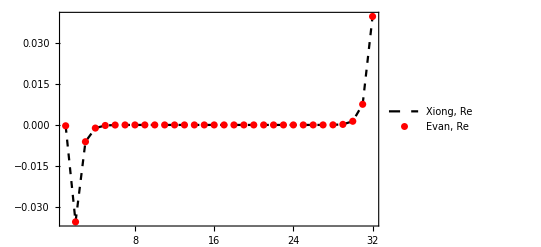
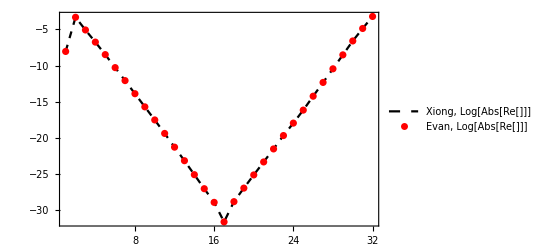
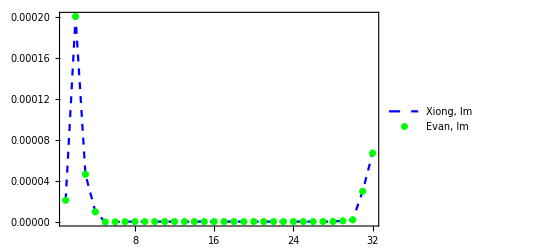
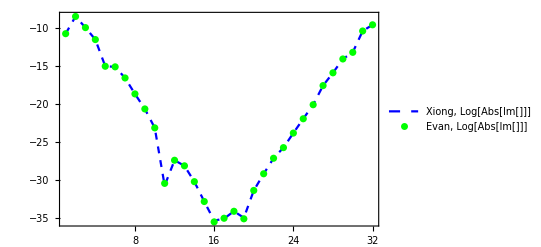
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x]\\psi(x)\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

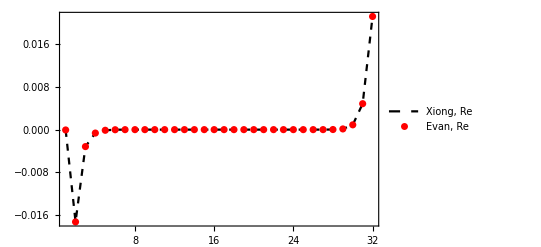
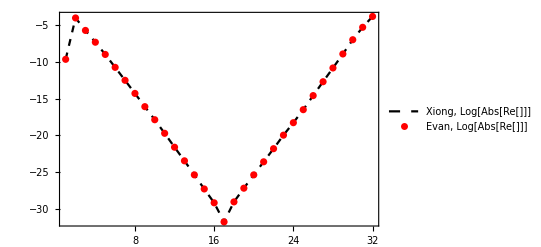
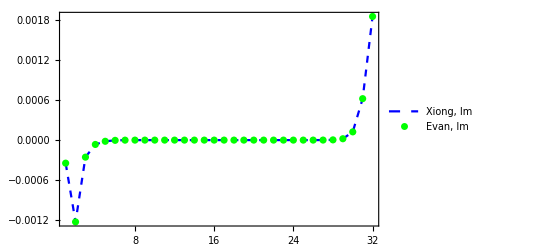
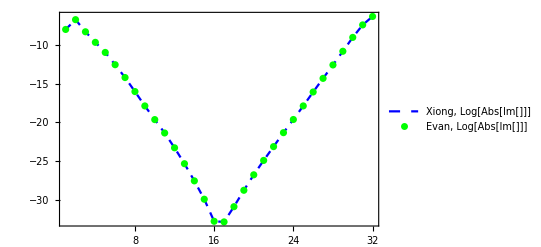
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-\\hat{z}]\\psi(x-\\hat{z})\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

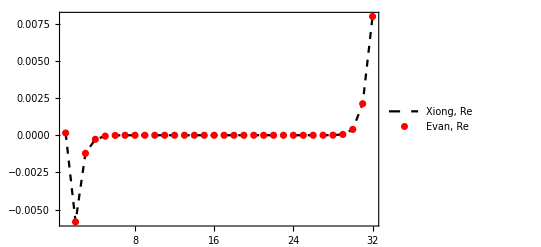
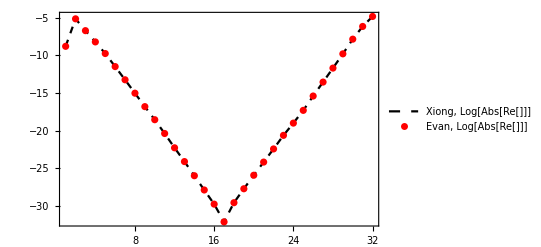
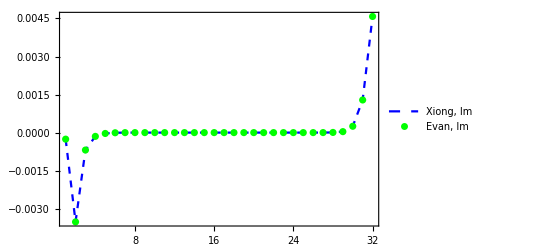
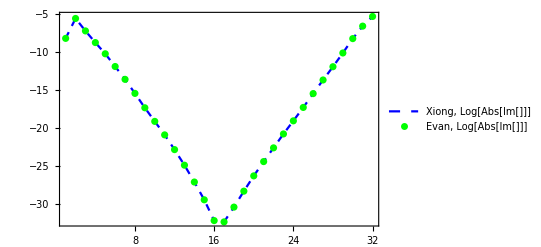
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

(1)⟦1,2,1,23⟧
 |  |  |  |

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_x\\langle\\pi^+(t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-2\\hat{z}]\\psi(x-2\\hat{z})\\right|\\pi^+(0)\\rangle}",Magnification->1.75],Top]
```

## correlation function Σ_x⟨π^+(t)|q̄(x)γ_z W[x,x+Δ_z]q(x+Δ_z)|π^+(0)⟩ , traced propagators

```mathematica
trPrpgtrsRe=Import["tr_prpgtrs.h5",{"Datasets","/Re"}];
```

```mathematica
trPrpgtrsIm=Import["tr_prpgtrs.h5",{"Datasets","/Im"}];
```

```mathematica
trPrpgtrs=Transpose[trPrpgtrsRe+I*trPrpgtrsIm,{4,3,2,1}];
```

```mathematica
{Nx,Ny,Nz,Nt}=Dimensions[trPrpgtrs]
```

{4,4,4,32}

```mathematica
mine=Table[ParallelSum[trPrpgtrs⟦i,j,k,t⟧,{i,Nx},{j,Ny},{k,Nz}],{t,Nt}]
```

{-0.000201179-0.000456713 ⅈ,0.00577913-0.00381964 ⅈ,0.00123821-0.000742693 ⅈ,0.000312654-0.000147241 ⅈ,0.0000695578-0.0000265091 ⅈ,0.0000122701-5.22249×10^-6 ⅈ,2.07835×10^-6-1.00646×10^-6 ⅈ,3.23017×10^-7-1.74017×10^-7 ⅈ,5.2606×10^-8-2.76186×10^-8 ⅈ,8.59082×10^-9-4.75304×10^-9 ⅈ,1.31157×10^-9-8.28387×10^-10 ⅈ,1.91606×10^-10-1.21777×10^-10 ⅈ,2.92546×10^-11-1.67624×10^-11 ⅈ,4.17799×10^-12-1.84114×10^-12 ⅈ,5.85874×10^-13-1.57042×10^-13 ⅈ,8.35903×10^-14-9.39631×10^-15 ⅈ,-1.78807×10^-14+8.75512×10^-15 ⅈ,-1.53013×10^-13+5.50085×10^-14 ⅈ,-9.92726×10^-13+4.20836×10^-13 ⅈ,-6.1651×10^-12+3.07045×10^-12 ⅈ,-3.68742×10^-11+1.99431×10^-11 ⅈ,-2.17257×10^-10+1.22273×10^-10 ⅈ,-1.34817×10^-9+7.55841×10^-10 ⅈ,-7.15736×10^-9+4.27477×10^-9 ⅈ,-4.04727×10^-8+2.61456×10^-8 ⅈ,-2.60401×10^-7+1.73026×10^-7 ⅈ,-1.65179×10^-6+1.02188×10^-6 ⅈ,-9.99734×10^-6+6.05958×10^-6 ⅈ,-0.0000666099+0.0000387494 ⅈ,-0.000453809+0.000259986 ⅈ,-0.00216519+0.00137517 ⅈ,-0.0084239+0.00449679 ⅈ}

```mathematica
MmntmPrjctdtrPrpgtrs[P_?((Head[#]==List)&&(Length[#_]==3)&)]:=Table[ParallelSum[E^(-I*2π*(P⟦1⟧*i/Nx+P⟦2⟧*j/Ny+P⟦3⟧*k/Nz))*trPrpgtrs⟦i,j,k,t⟧,{i,Nx},{j,Ny},{k,Nz}],{t,Nt}]
```

```mathematica
XiongPz=MmntmPrjctdtrPrpgtrs[{0,0,2}];
```

```mathematica
EvanPz=ToExpression[StringReplace["[-1.02985814e-04 +1.44262529e-04j  -1.87677684e-03 -1.04485134e-03j
  -3.06382668e-04 -1.45882475e-04j  -4.08867034e-05 -2.70715745e-05j
  -6.56182730e-06 -4.32378965e-06j  -7.51082848e-07 -5.09306053e-07j
  -2.19341071e-08 +6.04844805e-09j  -4.93523333e-09 -1.39422100e-09j
  -1.63333173e-09 -1.32578574e-09j  -1.50509786e-10 -1.45249134e-10j
  -6.22503335e-11 -5.39079043e-11j  -9.84399407e-12 -1.31644433e-11j
  -1.82801740e-12 -2.23955214e-12j  -1.74979546e-13 -2.40323005e-13j
  -3.76895459e-14 -3.01230043e-14j  -6.36095281e-15 -3.28649150e-15j
   2.28437170e-16 -4.71538664e-16j   3.80225463e-15 -1.28323759e-15j
   3.18997474e-14 -3.31951925e-15j   1.34017975e-13 -8.05233456e-14j
   2.79408765e-13 -1.08322541e-12j  -2.97894571e-13 -4.02027609e-12j
  -9.11928396e-12 -8.91340193e-12j  -3.17084648e-11 +2.22809665e-11j
  -9.65932231e-11 +8.44727795e-10j   1.80999550e-09 +3.68445863e-09j
   5.43254908e-08 +4.83009433e-08j   4.42315068e-07 +3.32556121e-07j
   4.55996068e-06 +2.78699293e-06j   3.49881577e-05 +2.93136808e-05j
   3.37146340e-04 +2.17108992e-04j   2.22603075e-03 +1.42853548e-03j]",{"["->"{","]"->"}","e"->"*^","  "->","," "->""}]]//.j->I;
```

```mathematica
ReEvan=ListPlot[EvanPz//Re,PlotStyle->Red,PlotLegends->{"Evan, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ReXng=ListPlot[XiongPz//Re,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Re"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImEvan=ListPlot[EvanPz//Im,PlotStyle->Green,PlotLegends->{"Evan, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
ImXng=ListPlot[XiongPz//Im,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Im"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReEvan=ListPlot[EvanPz//Re//Abs//Log,PlotStyle->Red,PlotLegends->{"Evan, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsReXng=ListPlot[XiongPz//Re//Abs//Log,PlotStyle->{Dashed,Black},Joined->True,PlotLegends->{"Xiong, Log[Abs[Re[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImEvan=ListPlot[EvanPz//Im//Abs//Log,PlotStyle->Green,PlotLegends->{"Evan, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

```mathematica
LogAbsImXng=ListPlot[XiongPz//Im//Abs//Log,PlotStyle->{Dashed,Blue},Joined->True,PlotLegends->{"Xiong, Log[Abs[Im[]]]"},PlotRange->All,Frame->True,Axes->False];
```

Show

```mathematica
<<MaTeX`
```

```mathematica
Labeled[Grid[{{Show[{ReXng,ReEvan},ImageSize->400],Show[{LogAbsReXng,LogAbsReEvan},PlotRange->All,ImageSize->400]},{Show[{ImXng,ImEvan},ImageSize->400],Show[{LogAbsImXng,LogAbsImEvan},PlotRange->All,ImageSize->400]}}],MaTeX["\\boldsymbol{\\sum_{xy} e^{i2\\hat{p}_zy}\\langle\\left.\\pi^+(y,t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-2\\hat{z}]\\psi(x-2\\hat{z})\\right|\\pi(0)\\right.\\rangle}",Magnification->1.75],Top]
```

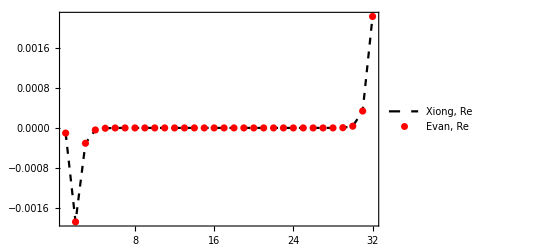
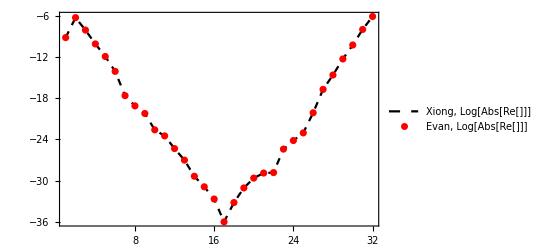
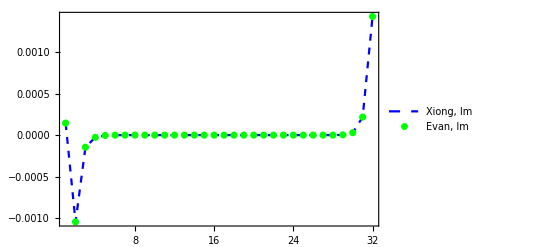
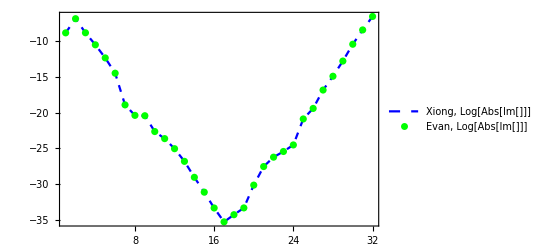
```mathematica
tt={{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}}-Graphics-;
```

```mathematica
Labeled[tt⟦1⟧,MaTeX["\\boldsymbol{\\sum_{xy} e^{i2\\hat{p}_zy}\\langle\\left.\\pi^+(y,t)\\left|\\bar{\\psi}(x)\\gamma_z W[x,x-2\\hat{z}]\\psi(x-2\\hat{z})\\right|\\pi(0)\\right.\\rangle}",Magnification->1.75],Top]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics-

```mathematica
Export["compare.png",%]
```

compare.png